# Primordial Gravitational Waves in Modified Gravity

```mathematica
ClearAll["Global`*"];
```

## Constants

```mathematica
h0 = 0.72;
H0 = 100*h0/300000;(*Quantity["km/(Mpc*s)"]*)
ωb0=0.02264;
ωm0=0.1138;
```

### Matter densities

```mathematica
Ωb[a_]:=ωb0/h0^2*a^-3(* baryonic matter *)
Ωm[a_]:=ωm0/h0^2*a^-3(* dark matter *)
Ωv[a_]:=1-((ωb0+ωm0)/h0^2)(* dark energy *)
```

### Hubble function

```mathematica
H[x_]:=H0*Sqrt[Ωb[a]+Ωm[a]+Ωv[a]]/.a->Exp[x];
Hconf[x_]:=H[x]*Exp[x];
```

## Amplitude of the pertubation

```mathematica
r=0.05;
k0=0.05;
AS=Exp[3.089442]*10^-10;
AT=r*AS;
nT=-r/8;
hA[k_]=Sqrt[AT*(k/k0)^nT];(* Amplitude *)
```

## Solution for constant αM

```mathematica
aInitial=10^-10;
sol=ParametricNDSolve[{h''[x]+(Hconf'[x]/Hconf[x]+2+αM)*h'[x]+(cT*k/Hconf[x])^2*h[x]==0,h[Log[aInitial]]==1,h'[Log[aInitial]]==0},h,{x,Log[aInitial],0},{k,cT,αM}];
ha[k_,cT_,αM_][a_]=hA[k]*h[k,cT,αM][x]/.sol/.x->Log[a];
```

### Varying αM

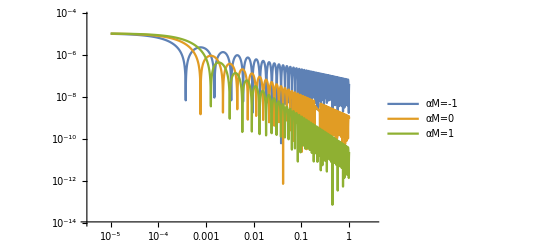

```mathematica
LogLogPlot[Evaluate[Table[Abs[ha[0.01,1,αM][a]],{αM,-1,1,1}]],{a,10^-5,1},PlotLegends->Placed[{"αM=-1","αM=0","αM=1"},Right]]
```

Increasing αM introduces more friction, so the amplitude of the gravitational wave decreases more rapidly.

### Varying k

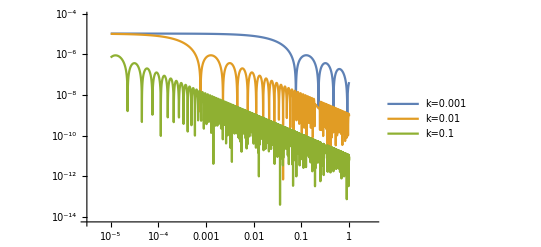

```mathematica
LogLogPlot[Evaluate[Table[Abs[ha[k,1,0][a]],{k,{0.001,0.01,0.1}}]],{a,10^-5,1},PlotLegends->Placed[{"k=0.001","k=0.01","k=0.1"},Right]]
```

The gravitational wave enters the horizon earlier for larger modes k.

### Varying cT

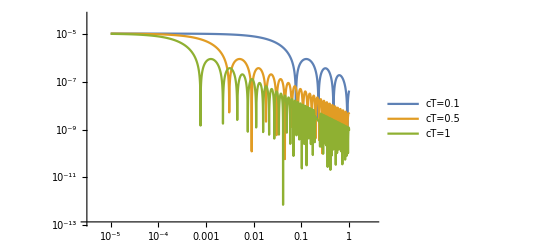

```mathematica
LogLogPlot[Evaluate[Table[Abs[ha[0.01,cT,0][a]],{cT,{0.1,0.5,1}}]],{a,10^-5,1},PlotLegends->Placed[{"cT=0.1","cT=0.5","cT=1"},Right]]
```

For a slower propagation, the wave enters the horizon later.

## Solution for parametrized αM

```mathematica
αM[αM0_,β_][x_]:=αM0*Exp[x*β];
aInitial=10^-10;
sol=ParametricNDSolve[{h''[x]+(Hconf'[x]/Hconf[x]+2+αM[αM0,β][x])*h'[x]+(cT*k/Hconf[x])^2*h[x]==0,h[Log[aInitial]]==1,h'[Log[aInitial]]==0},h,{x,Log[aInitial],0},{αM0,β,cT,k}];
haβ[αM0_,β_,cT_,k_][a_]=hA[k]*h[αM0,β,cT,k][x]/.sol/.x->Log[a];
```

### Varying β

#### αM0=-1

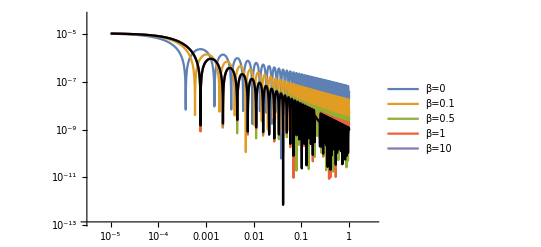

```mathematica
αM0Plot=LogLogPlot[Evaluate[Abs[haβ[0,0,1,0.01][a]]],{a,10^-5,1},PlotStyle->Directive[Thick,Black],PlotLegends->Placed[{"αM0=0"},Left]];
Show[LogLogPlot[Evaluate[Table[Abs[haβ[-1,β,1,0.01][a]],{β,{0,0.1,0.5,1,10}}]],{a,10^-5,1},PlotLegends->Placed[{"β=0","β=0.1","β=0.5","β=1","β=10"},Right]],αM0Plot]
```

#### αM0=1

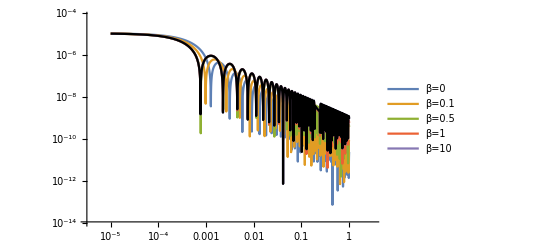

```mathematica
Show[LogLogPlot[Evaluate[Table[Abs[haβ[1,β,1,0.01][a]],{β,{0,0.1,0.5,1,10}}]],{a,10^-5,1},PlotLegends->Placed[{"β=0","β=0.1","β=0.5","β=1","β=10"},Right]],αM0Plot]
```

For larger β the curve converges to αM=0 at early times and deviates at late times.

### Varying αM0 for some β’s

```mathematica
αM0List={-2,-1,0,1,2};
αM0ListLegends={"αM0=-2","αM0=-1","αM0=0","αM0=1","αM0=2"};
```

#### β=0

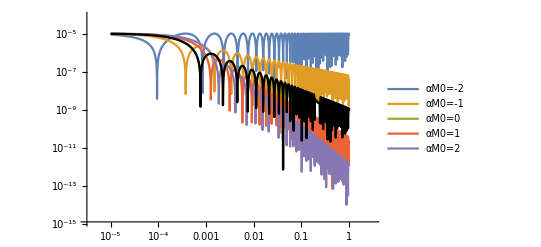

```mathematica
Show[LogLogPlot[Evaluate[Table[Abs[haβ[αM0,0,1,0.01][a]],{αM0,αM0List}]],{a,10^-5,1},PlotLegends->Placed[αM0ListLegends,Right]],αM0Plot]
```

#### β=0.5

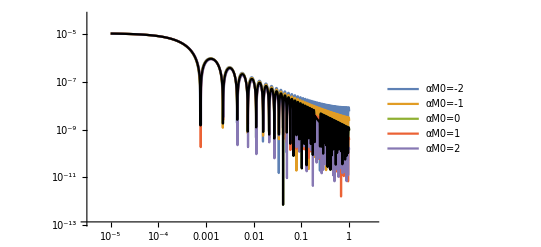

```mathematica
Show[LogLogPlot[Evaluate[Table[Abs[haβ[αM0,0.5,1,0.01][a]],{αM0,αM0List}]],{a,10^-5,1},PlotLegends->Placed[αM0ListLegends,Right]],αM0Plot]
```

#### β=1

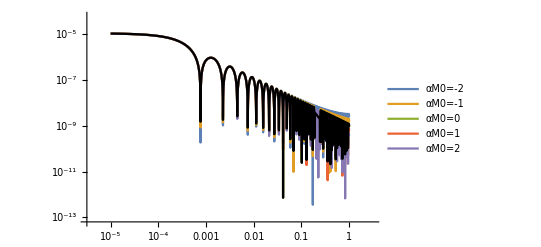

```mathematica
Show[LogLogPlot[Evaluate[Table[Abs[haβ[αM0,1,1,0.01][a]],{αM0,αM0List}]],{a,10^-5,1},PlotLegends->Placed[αM0ListLegends,Right]],αM0Plot]
```

## Slope of the Amplitude

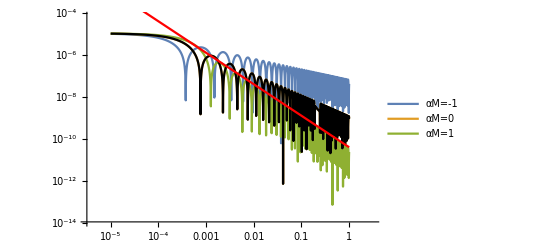

```mathematica
hSlope[a_][αM_]:=a^(-1-αM/2)
Show[LogLogPlot[Evaluate[Table[Abs[haβ[αM0,0,1,0.01][a]],{αM0,{-1,0,1}}]],{a,10^-5,1},PlotLegends->Placed[{"αM=-1","αM=0","αM=1"},Right]],αM0Plot,LogLogPlot[hSlope[a][1]*10^(-10.4),{a,10^-5,1},PlotStyle->Directive[Thick,Red]]]
```

### Growing amplitude for αM<-2

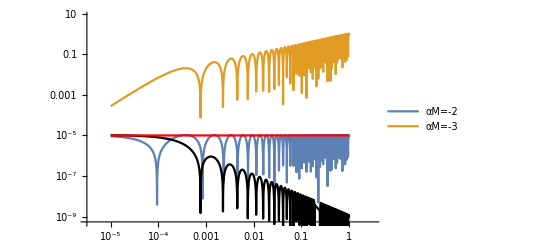

```mathematica
Show[LogLogPlot[Evaluate[Table[Abs[haβ[αM0,0,1,0.01][a]],{αM0,{-2,-3}}]],{a,10^-5,1},PlotLegends->Placed[{"αM=-2","αM=-3"},Right]],αM0Plot,LogLogPlot[hSlope[a][-2]*10^(-5),{a,10^-5,1},PlotStyle->Directive[Thick,Red]]]
```

## 2-metric coupling

{αMg→0,αMf→-3,cTg→1,cTf→1,k→0.01,mg→0,mf→0,qg→1/100000,qf→0}

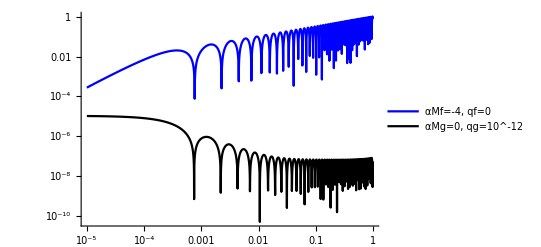

```mathematica
eqg=hg''[x]+(Hconf'[x]/Hconf[x]+2+αMg)*hg'[x]+(mg^2+cTg*k/Hconf[x])^2*hg[x];
eqf=hf''[x]+(Hconf'[x]/Hconf[x]+2+αMf)*hf'[x]+(mf^2+cTf*k/Hconf[x])^2*hf[x];
sol=ParametricNDSolve[{eqg==qg*hf[x],eqf==qf*hg[x],hg[Log[aInitial]]==1,hg'[Log[aInitial]]==0,hf[Log[aInitial]]==1,hf'[Log[aInitial]]==0},{hg,hf},{x,Log[aInitial],0},{αMg,αMf,cTg,cTf,k,mg,mf,qg,qf}];
hga[αMg_,αMf_,cTg_,cTf_,k_,mg_,mf_,qg_,qf_][a_]=hA[k]*hg[αMg,αMf,cTg,cTf,k,mg,mf,qg,qf][x]/.sol/.x->Log[a];
hfa[αMg_,αMf_,cTg_,cTf_,k_,mg_,mf_,qg_,qf_][a_]=hA[k]*hf[αMg,αMf,cTg,cTf,k,mg,mf,qg,qf][x]/.sol/.x->Log[a];
(*params={αMg->0,αMf->-4,cTg->1,cTf->1,k->0.01,mg->10^-12,mf->0,qg->10^-12,qf->0}*)
params={αMg->0,αMf->-3,cTg->1,cTf->1,k->0.01,mg->0,mf->0,qg->10^-5,qf->0}
Show[LogLogPlot[Abs[hfa[αMg,αMf,cTg,cTf,k,mg,mf,qg,qf][a]/.params],{a,10^-5,1},PlotLegends->Placed[{"αMf=-4, qf=0"},Right],PlotStyle->Directive[Thick,Blue]],LogLogPlot[Abs[hga[αMg,αMf,cTg,cTf,k,mg,mf,qg,qf][a]/.params],{a,10^-5,1},PlotLegends->Placed[{"αMg=0, qg=10^-12"},Right],PlotStyle->Directive[Thick,Black]],PlotRange->Automatic]
```